## Question 3

### 3.1 - Adjacency Matrix

#### Nodal diagram

( | E_in | E_x1 | E_xcav | E_xcav2 | E_xrefl | E_y1 | E_ycav | E_ycav2 | E_yrefl | E_as | E_refl
E_in | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
E_x1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
E_xcav | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
E_xcav2 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
E_xrefl | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
E_y1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
E_ycav | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
E_ycav2 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
E_yrefl | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
E_as | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
E_refl | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0)

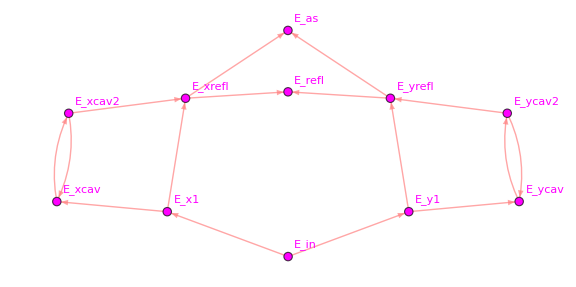

```mathematica
nodes={"E_in",
"E_x1",
"E_xcav",
"E_xcav2",
"E_xrefl",
"E_y1",
"E_ycav",
"E_ycav2",
"E_yrefl",
"E_as",
"E_refl"};

A={                   (*in x1 xc xc2 xr y1 yc yc2 yr as r*)
  (*E_in*)    {0,0,0, 0,    0,0,  0,0,    0,0,0},
(*E_x1*)      {1,0,0, 0,    0,0,  0,0,    0,0,0},
(*E_xcav*)  {0,1,0, 1,   0,0,  0,0,    0,0,0},
(*E_xcav2*){0,0,1, 0,   0,0,  0,0,    0,0,0},
(*E_xrefl*){0,1,0, 1,   0,0,  0,0,    0,0,0},
(*E_y1*)       {1,0,0, 0,   0,0,  0,0,    0,0,0},
(*E_ycav*)  {0,0,0, 0,   0,1,  0,1,    0,0,0},
(*E_ycav2*){0,0,0, 0,   0,0,  1,0,    0,0,0},
(*E_yrefl*){0,0,0, 0,   0,1,  0,1,    0,0,0},
(*E_as*)       {0,0,0, 0,   1,0,  0,0,    1,0,0},
(*E_refl*)  {0,0,0, 0,   1,0,  0,0,    1,0,0}};


MatrixForm[A,TableHeadings->{nodes,nodes}]

(*directed graph to help me visualize*)
edges=Flatten[Table[If[A[[i,j]]==1,DirectedEdge[nodes[[j]],nodes[[i]]],Nothing],{j,Length[nodes]},{i,Length[nodes]}]];

Graph[edges,VertexLabels->"Name",ImageSize->Large,EdgeStyle->Pink,VertexStyle->Magenta]
```

#### Actual matrix

```mathematica
nodes={"E_in",
"E_x1",
"E_xcav",
"E_xcav2",
"E_xrefl",
"E_y1",
"E_ycav",
"E_ycav2",
"E_yrefl",
"E_as",
"E_refl"};

M={                   (*in x1 xc xc2 xr y1 yc yc2 yr as r*)
  (*E_in*)    {0,0,0, 0,    0,0,  0,0,    0,0,0},
(*E_x1*)      {tbs*Exp[I*ϕx],0,0, 0,    0,0,  0,0,    0,0,0},
(*E_xcav*)  {0,txin,0, -rxin*Exp[I*Φx],   0,0,  0,0,    0,0,0},
(*E_xcav2*){0,0,-rxend*Exp[I*Φx], 0,   0,0,  0,0,    0,0,0},
(*E_xrefl*){0,rxin,0, txin,   0,0,  0,0,    0,0,0},
(*E_y1*)       {-rbs*Exp[I*ϕy],0,0, 0,   0,0,  0,0,    0,0,0},
(*E_ycav*)  {0,0,0, 0,   0,tyin,  0,-ryin*Exp[I*Φy],    0,0,0},
(*E_ycav2*){0,0,0, 0,   0,0,  -ryend*Exp[I*Φy],0,    0,0,0},
(*E_yrefl*){0,0,0, 0,   0,ryin,  0,tyin,    0,0,0},
(*E_as*)       {0,0,0, 0,   rbs*Exp[I*ϕx],0,  0,0,    tbs*Exp[I*ϕy],0,0},
(*E_refl*)  {0,0,0, 0,   tbs*Exp[I*ϕx],0,  0,0,    -rbs*Exp[I*ϕy],0,0}};

MatrixForm[M,TableHeadings->{nodes,nodes}]
```

( | E_in | E_x1 | E_xcav | E_xcav2 | E_xrefl | E_y1 | E_ycav | E_ycav2 | E_yrefl | E_as | E_refl
E_in | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
E_x1 | ⅇ^(ⅈ ϕx) tbs | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
E_xcav | 0 | txin | 0 | -ⅇ^(ⅈ Φx) rxin | 0 | 0 | 0 | 0 | 0 | 0 | 0
E_xcav2 | 0 | 0 | -ⅇ^(ⅈ Φx) rxend | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
E_xrefl | 0 | rxin | 0 | txin | 0 | 0 | 0 | 0 | 0 | 0 | 0
E_y1 | -ⅇ^(ⅈ ϕy) rbs | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
E_ycav | 0 | 0 | 0 | 0 | 0 | tyin | 0 | -ⅇ^(ⅈ Φy) ryin | 0 | 0 | 0
E_ycav2 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅇ^(ⅈ Φy) ryend | 0 | 0 | 0 | 0
E_yrefl | 0 | 0 | 0 | 0 | 0 | ryin | 0 | tyin | 0 | 0 | 0
E_as | 0 | 0 | 0 | 0 | ⅇ^(ⅈ ϕx) rbs | 0 | 0 | 0 | ⅇ^(ⅈ ϕy) tbs | 0 | 0
E_refl | 0 | 0 | 0 | 0 | ⅇ^(ⅈ ϕx) tbs | 0 | 0 | 0 | -ⅇ^(ⅈ ϕy) rbs | 0 | 0)

### 3.2 - Antisymmetric Port Field Derivations

```mathematica
id=IdentityMatrix[Length[nodes]];
IminusM=id-M;
T=Inverse[IminusM];


MatrixForm[T,TableHeadings->{nodes,nodes}]

T[[Position[nodes,"E_as"][[1,1]],Position[nodes,"E_in"][[1,1]]]]

TF[from_String,to_String]:=T[[Position[nodes,to][[1,1]],Position[nodes,from][[1,1]]]]

Print["E_as/E_in = ",FullSimplify[TF["E_in","E_as"]]]
```

( | E_in | E_x1 | E_xcav | E_xcav2 | E_xrefl | E_y1 | E_ycav | E_ycav2 | E_yrefl | E_as | E_refl
E_in | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
E_x1 | (ⅇ^(ⅈ ϕx) tbs-ⅇ^(ⅈ ϕx+2 ⅈ Φx) rxend rxin tbs-ⅇ^(ⅈ ϕx+2 ⅈ Φy) ryend ryin tbs+ⅇ^(ⅈ ϕx+2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin tbs)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
E_xcav | (ⅇ^(ⅈ ϕx) tbs txin-ⅇ^(ⅈ ϕx+2 ⅈ Φy) ryend ryin tbs txin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (txin-ⅇ^(2 ⅈ Φy) ryend ryin txin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (1-ⅇ^(2 ⅈ Φy) ryend ryin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (-ⅇ^(ⅈ Φx) rxin+ⅇ^(ⅈ Φx+2 ⅈ Φy) rxin ryend ryin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | 0 | 0 | 0 | 0 | 0 | 0 | 0
E_xcav2 | (-ⅇ^(ⅈ ϕx+ⅈ Φx) rxend tbs txin+ⅇ^(ⅈ ϕx+ⅈ Φx+2 ⅈ Φy) rxend ryend ryin tbs txin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (-ⅇ^(ⅈ Φx) rxend txin+ⅇ^(ⅈ Φx+2 ⅈ Φy) rxend ryend ryin txin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (-ⅇ^(ⅈ Φx) rxend+ⅇ^(ⅈ Φx+2 ⅈ Φy) rxend ryend ryin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (1-ⅇ^(2 ⅈ Φy) ryend ryin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | 0 | 0 | 0 | 0 | 0 | 0 | 0
E_xrefl | (ⅇ^(ⅈ ϕx) rxin tbs-ⅇ^(ⅈ ϕx+2 ⅈ Φx) rxend rxin^2 tbs-ⅇ^(ⅈ ϕx+2 ⅈ Φy) rxin ryend ryin tbs+ⅇ^(ⅈ ϕx+2 ⅈ Φx+2 ⅈ Φy) rxend rxin^2 ryend ryin tbs-ⅇ^(ⅈ ϕx+ⅈ Φx) rxend tbs txin^2+ⅇ^(ⅈ ϕx+ⅈ Φx+2 ⅈ Φy) rxend ryend ryin tbs txin^2)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (rxin-ⅇ^(2 ⅈ Φx) rxend rxin^2-ⅇ^(2 ⅈ Φy) rxin ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin^2 ryend ryin-ⅇ^(ⅈ Φx) rxend txin^2+ⅇ^(ⅈ Φx+2 ⅈ Φy) rxend ryend ryin txin^2)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (-ⅇ^(ⅈ Φx) rxend txin+ⅇ^(ⅈ Φx+2 ⅈ Φy) rxend ryend ryin txin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (txin-ⅇ^(2 ⅈ Φy) ryend ryin txin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | 1 | 0 | 0 | 0 | 0 | 0 | 0
E_y1 | (-ⅇ^(ⅈ ϕy) rbs+ⅇ^(2 ⅈ Φx+ⅈ ϕy) rbs rxend rxin+ⅇ^(ⅈ ϕy+2 ⅈ Φy) rbs ryend ryin-ⅇ^(2 ⅈ Φx+ⅈ ϕy+2 ⅈ Φy) rbs rxend rxin ryend ryin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
E_ycav | (-ⅇ^(ⅈ ϕy) rbs tyin+ⅇ^(2 ⅈ Φx+ⅈ ϕy) rbs rxend rxin tyin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | 0 | 0 | 0 | 0 | (tyin-ⅇ^(2 ⅈ Φx) rxend rxin tyin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (1-ⅇ^(2 ⅈ Φx) rxend rxin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (-ⅇ^(ⅈ Φy) ryin+ⅇ^(2 ⅈ Φx+ⅈ Φy) rxend rxin ryin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | 0 | 0 | 0
E_ycav2 | (ⅇ^(ⅈ ϕy+ⅈ Φy) rbs ryend tyin-ⅇ^(2 ⅈ Φx+ⅈ ϕy+ⅈ Φy) rbs rxend rxin ryend tyin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | 0 | 0 | 0 | 0 | (-ⅇ^(ⅈ Φy) ryend tyin+ⅇ^(2 ⅈ Φx+ⅈ Φy) rxend rxin ryend tyin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (-ⅇ^(ⅈ Φy) ryend+ⅇ^(2 ⅈ Φx+ⅈ Φy) rxend rxin ryend)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (1-ⅇ^(2 ⅈ Φx) rxend rxin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | 0 | 0 | 0
E_yrefl | (-ⅇ^(ⅈ ϕy) rbs ryin+ⅇ^(2 ⅈ Φx+ⅈ ϕy) rbs rxend rxin ryin+ⅇ^(ⅈ ϕy+2 ⅈ Φy) rbs ryend ryin^2-ⅇ^(2 ⅈ Φx+ⅈ ϕy+2 ⅈ Φy) rbs rxend rxin ryend ryin^2+ⅇ^(ⅈ ϕy+ⅈ Φy) rbs ryend tyin^2-ⅇ^(2 ⅈ Φx+ⅈ ϕy+ⅈ Φy) rbs rxend rxin ryend tyin^2)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | 0 | 0 | 0 | 0 | (ryin-ⅇ^(2 ⅈ Φx) rxend rxin ryin-ⅇ^(2 ⅈ Φy) ryend ryin^2+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin^2-ⅇ^(ⅈ Φy) ryend tyin^2+ⅇ^(2 ⅈ Φx+ⅈ Φy) rxend rxin ryend tyin^2)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (-ⅇ^(ⅈ Φy) ryend tyin+ⅇ^(2 ⅈ Φx+ⅈ Φy) rxend rxin ryend tyin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (tyin-ⅇ^(2 ⅈ Φx) rxend rxin tyin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | 1 | 0 | 0
E_as | (ⅇ^(2 ⅈ ϕx) rbs rxin tbs-ⅇ^(2 ⅈ ϕx+2 ⅈ Φx) rbs rxend rxin^2 tbs-ⅇ^(2 ⅈ ϕy) rbs ryin tbs+ⅇ^(2 ⅈ Φx+2 ⅈ ϕy) rbs rxend rxin ryin tbs-ⅇ^(2 ⅈ ϕx+2 ⅈ Φy) rbs rxin ryend ryin tbs+ⅇ^(2 ⅈ ϕx+2 ⅈ Φx+2 ⅈ Φy) rbs rxend rxin^2 ryend ryin tbs+ⅇ^(2 ⅈ ϕy+2 ⅈ Φy) rbs ryend ryin^2 tbs-ⅇ^(2 ⅈ Φx+2 ⅈ ϕy+2 ⅈ Φy) rbs rxend rxin ryend ryin^2 tbs-ⅇ^(2 ⅈ ϕx+ⅈ Φx) rbs rxend tbs txin^2+ⅇ^(2 ⅈ ϕx+ⅈ Φx+2 ⅈ Φy) rbs rxend ryend ryin tbs txin^2+ⅇ^(2 ⅈ ϕy+ⅈ Φy) rbs ryend tbs tyin^2-ⅇ^(2 ⅈ Φx+2 ⅈ ϕy+ⅈ Φy) rbs rxend rxin ryend tbs tyin^2)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (ⅇ^(ⅈ ϕx) rbs rxin-ⅇ^(ⅈ ϕx+2 ⅈ Φx) rbs rxend rxin^2-ⅇ^(ⅈ ϕx+2 ⅈ Φy) rbs rxin ryend ryin+ⅇ^(ⅈ ϕx+2 ⅈ Φx+2 ⅈ Φy) rbs rxend rxin^2 ryend ryin-ⅇ^(ⅈ ϕx+ⅈ Φx) rbs rxend txin^2+ⅇ^(ⅈ ϕx+ⅈ Φx+2 ⅈ Φy) rbs rxend ryend ryin txin^2)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (-ⅇ^(ⅈ ϕx+ⅈ Φx) rbs rxend txin+ⅇ^(ⅈ ϕx+ⅈ Φx+2 ⅈ Φy) rbs rxend ryend ryin txin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (ⅇ^(ⅈ ϕx) rbs txin-ⅇ^(ⅈ ϕx+2 ⅈ Φy) rbs ryend ryin txin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (ⅇ^(ⅈ ϕx) rbs-ⅇ^(ⅈ ϕx+2 ⅈ Φx) rbs rxend rxin-ⅇ^(ⅈ ϕx+2 ⅈ Φy) rbs ryend ryin+ⅇ^(ⅈ ϕx+2 ⅈ Φx+2 ⅈ Φy) rbs rxend rxin ryend ryin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (ⅇ^(ⅈ ϕy) ryin tbs-ⅇ^(2 ⅈ Φx+ⅈ ϕy) rxend rxin ryin tbs-ⅇ^(ⅈ ϕy+2 ⅈ Φy) ryend ryin^2 tbs+ⅇ^(2 ⅈ Φx+ⅈ ϕy+2 ⅈ Φy) rxend rxin ryend ryin^2 tbs-ⅇ^(ⅈ ϕy+ⅈ Φy) ryend tbs tyin^2+ⅇ^(2 ⅈ Φx+ⅈ ϕy+ⅈ Φy) rxend rxin ryend tbs tyin^2)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (-ⅇ^(ⅈ ϕy+ⅈ Φy) ryend tbs tyin+ⅇ^(2 ⅈ Φx+ⅈ ϕy+ⅈ Φy) rxend rxin ryend tbs tyin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (ⅇ^(ⅈ ϕy) tbs tyin-ⅇ^(2 ⅈ Φx+ⅈ ϕy) rxend rxin tbs tyin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (ⅇ^(ⅈ ϕy) tbs-ⅇ^(2 ⅈ Φx+ⅈ ϕy) rxend rxin tbs-ⅇ^(ⅈ ϕy+2 ⅈ Φy) ryend ryin tbs+ⅇ^(2 ⅈ Φx+ⅈ ϕy+2 ⅈ Φy) rxend rxin ryend ryin tbs)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | 1 | 0
E_refl | (ⅇ^(2 ⅈ ϕy) rbs^2 ryin-ⅇ^(2 ⅈ Φx+2 ⅈ ϕy) rbs^2 rxend rxin ryin-ⅇ^(2 ⅈ ϕy+2 ⅈ Φy) rbs^2 ryend ryin^2+ⅇ^(2 ⅈ Φx+2 ⅈ ϕy+2 ⅈ Φy) rbs^2 rxend rxin ryend ryin^2+ⅇ^(2 ⅈ ϕx) rxin tbs^2-ⅇ^(2 ⅈ ϕx+2 ⅈ Φx) rxend rxin^2 tbs^2-ⅇ^(2 ⅈ ϕx+2 ⅈ Φy) rxin ryend ryin tbs^2+ⅇ^(2 ⅈ ϕx+2 ⅈ Φx+2 ⅈ Φy) rxend rxin^2 ryend ryin tbs^2-ⅇ^(2 ⅈ ϕx+ⅈ Φx) rxend tbs^2 txin^2+ⅇ^(2 ⅈ ϕx+ⅈ Φx+2 ⅈ Φy) rxend ryend ryin tbs^2 txin^2-ⅇ^(2 ⅈ ϕy+ⅈ Φy) rbs^2 ryend tyin^2+ⅇ^(2 ⅈ Φx+2 ⅈ ϕy+ⅈ Φy) rbs^2 rxend rxin ryend tyin^2)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (ⅇ^(ⅈ ϕx) rxin tbs-ⅇ^(ⅈ ϕx+2 ⅈ Φx) rxend rxin^2 tbs-ⅇ^(ⅈ ϕx+2 ⅈ Φy) rxin ryend ryin tbs+ⅇ^(ⅈ ϕx+2 ⅈ Φx+2 ⅈ Φy) rxend rxin^2 ryend ryin tbs-ⅇ^(ⅈ ϕx+ⅈ Φx) rxend tbs txin^2+ⅇ^(ⅈ ϕx+ⅈ Φx+2 ⅈ Φy) rxend ryend ryin tbs txin^2)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (-ⅇ^(ⅈ ϕx+ⅈ Φx) rxend tbs txin+ⅇ^(ⅈ ϕx+ⅈ Φx+2 ⅈ Φy) rxend ryend ryin tbs txin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (ⅇ^(ⅈ ϕx) tbs txin-ⅇ^(ⅈ ϕx+2 ⅈ Φy) ryend ryin tbs txin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (ⅇ^(ⅈ ϕx) tbs-ⅇ^(ⅈ ϕx+2 ⅈ Φx) rxend rxin tbs-ⅇ^(ⅈ ϕx+2 ⅈ Φy) ryend ryin tbs+ⅇ^(ⅈ ϕx+2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin tbs)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (-ⅇ^(ⅈ ϕy) rbs ryin+ⅇ^(2 ⅈ Φx+ⅈ ϕy) rbs rxend rxin ryin+ⅇ^(ⅈ ϕy+2 ⅈ Φy) rbs ryend ryin^2-ⅇ^(2 ⅈ Φx+ⅈ ϕy+2 ⅈ Φy) rbs rxend rxin ryend ryin^2+ⅇ^(ⅈ ϕy+ⅈ Φy) rbs ryend tyin^2-ⅇ^(2 ⅈ Φx+ⅈ ϕy+ⅈ Φy) rbs rxend rxin ryend tyin^2)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (ⅇ^(ⅈ ϕy+ⅈ Φy) rbs ryend tyin-ⅇ^(2 ⅈ Φx+ⅈ ϕy+ⅈ Φy) rbs rxend rxin ryend tyin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (-ⅇ^(ⅈ ϕy) rbs tyin+ⅇ^(2 ⅈ Φx+ⅈ ϕy) rbs rxend rxin tyin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | (-ⅇ^(ⅈ ϕy) rbs+ⅇ^(2 ⅈ Φx+ⅈ ϕy) rbs rxend rxin+ⅇ^(ⅈ ϕy+2 ⅈ Φy) rbs ryend ryin-ⅇ^(2 ⅈ Φx+ⅈ ϕy+2 ⅈ Φy) rbs rxend rxin ryend ryin)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin) | 0 | 1)

(ⅇ^(2 ⅈ ϕx) rbs rxin tbs-ⅇ^(2 ⅈ ϕx+2 ⅈ Φx) rbs rxend rxin^2 tbs-ⅇ^(2 ⅈ ϕy) rbs ryin tbs+ⅇ^(2 ⅈ Φx+2 ⅈ ϕy) rbs rxend rxin ryin tbs-ⅇ^(2 ⅈ ϕx+2 ⅈ Φy) rbs rxin ryend ryin tbs+ⅇ^(2 ⅈ ϕx+2 ⅈ Φx+2 ⅈ Φy) rbs rxend rxin^2 ryend ryin tbs+ⅇ^(2 ⅈ ϕy+2 ⅈ Φy) rbs ryend ryin^2 tbs-ⅇ^(2 ⅈ Φx+2 ⅈ ϕy+2 ⅈ Φy) rbs rxend rxin ryend ryin^2 tbs-ⅇ^(2 ⅈ ϕx+ⅈ Φx) rbs rxend tbs txin^2+ⅇ^(2 ⅈ ϕx+ⅈ Φx+2 ⅈ Φy) rbs rxend ryend ryin tbs txin^2+ⅇ^(2 ⅈ ϕy+ⅈ Φy) rbs ryend tbs tyin^2-ⅇ^(2 ⅈ Φx+2 ⅈ ϕy+ⅈ Φy) rbs rxend rxin ryend tbs tyin^2)/(1-ⅇ^(2 ⅈ Φx) rxend rxin-ⅇ^(2 ⅈ Φy) ryend ryin+ⅇ^(2 ⅈ Φx+2 ⅈ Φy) rxend rxin ryend ryin)

E_as/E_in = ((rbs tbs (ⅇ^(2 ⅈ ϕx) rxin-ⅇ^(2 ⅈ (ϕx+Φx)) rxend rxin^2-ⅇ^(2 ⅈ ϕy) ryin+ⅇ^(2 ⅈ (Φx+ϕy)) rxend rxin ryin-ⅇ^(2 ⅈ (ϕx+Φy)) rxin ryend ryin+ⅇ^(2 ⅈ (ϕx+Φx+Φy)) rxend rxin^2 ryend ryin+ⅇ^(2 ⅈ (ϕy+Φy)) ryend ryin^2-ⅇ^(2 ⅈ (Φx+ϕy+Φy)) rxend rxin ryend ryin^2-ⅇ^(ⅈ (2 ϕx+Φx)) rxend txin^2+ⅇ^(ⅈ (2 ϕx+Φx+2 Φy)) rxend ryend ryin txin^2+ⅇ^(ⅈ (2 ϕy+Φy)) ryend tyin^2-ⅇ^(ⅈ (2 (Φx+ϕy)+Φy)) rxend rxin ryend tyin^2))/((-1+ⅇ^(2 ⅈ Φx) rxend rxin) (-1+ⅇ^(2 ⅈ Φy) ryend ryin)))

### 3.3 - E_as Simplifications

```mathematica
stuffSub={rbs->1/Sqrt[2],tbs->1/Sqrt[2],rxend->r2,ryend->r2, rxin-> r1, ryin->r1,txin-> t1, tyin->t1};
phaseSub={Φx->Φc+Φd,Φy->Φc-Φd,ϕx->0, ϕy->0};

Print["E_as/E_in = ",FullSimplify[TF["E_in","E_as"]/. phaseSub/. stuffSub]]
```

E_as/E_in = (ⅇ^(ⅈ (Φc+Φd)) (-1+ⅇ^(2 ⅈ Φd)) r2 (1+ⅇ^(2 ⅈ Φc) r1 r2) t1^2)/(2 (ⅇ^(2 ⅈ Φd)-ⅇ^(2 ⅈ Φc) r1 r2) (-1+ⅇ^(2 ⅈ (Φc+Φd)) r1 r2))

### 3.4 - Interpretation

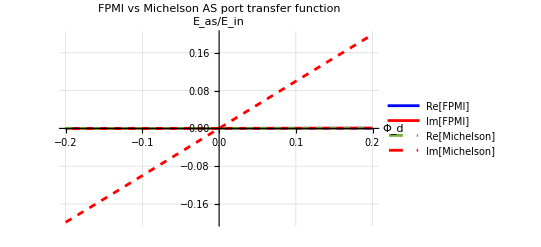

```mathematica
(*Parameters*)paramSub={r1->Sqrt[1-0.10],(*ITM:T=10% so r=sqrt(0.9)*)r2->1,(*ETM:T=0,perfect mirror*)t1->Sqrt[0.10],(*ITM:t=sqrt(T)*)lx->5,ly->5,(*short Michelson arms[m]*)Lx->4000,Ly->4000,(*FP arm lengths[m]*)λ->1064*10^-9  (*wavelength[m]*)};

k=2*Pi/(λ/. paramSub);

(*Common and differential phases*)
(*Φc=k*(Lx+Ly)/2,Φd sweeps*)
PhicVal=k*(4000);   (*symmetric arms so Φc=k*L*)

(*Transfer function*)
TFexpr=(Exp[I*(Φc+Φd)]*(-1+Exp[2*I*Φd])*r2*(1+Exp[2*I*Φc]*r1*r2)*t1^2)/(2*(Exp[2*I*Φd]-Exp[2*I*Φc]*r1*r2)*(-1+Exp[2*I*(Φc+Φd)]*r1*r2));

TFsub=TFexpr/. {r1->Sqrt[0.9],r2->1,t1->Sqrt[0.1],Φc->PhicVal};

(*Simple Michelson TF for comparison (no arm cavities)*)
(*E_as/E_in=(1/2)(e^{2iφx}-e^{2iφy})->i*sin(Φd) at Φc=0*)
TFmich=I*Sin[Φd];

(*Plot over a few linewidths around Φd=0*)
(*Cavity linewidth:δΦ~T/(2)=0.05 rad*)
PhidRange=0.2;

Plot[{Re[TFsub],Im[TFsub],Re[TFmich],Im[TFmich]},{Φd,-PhidRange,PhidRange},PlotLegends->{"Re[FPMI]","Im[FPMI]","Re[Michelson]","Im[Michelson]"},PlotStyle->{Blue,Red,Dashed,{Red,Dashed}},AxesLabel->{"\!\(\*SubscriptBox[\(Φ\), \(d\)]\)","\!\(\*FractionBox[\(E_as\), \(E_in\)]\)"},PlotLabel->"FPMI vs Michelson AS port transfer function",GridLines->Automatic,PlotRange->All]
```